# Hilltop Potential

```mathematica
Clear["Global`*"]
```

First we will define our potential: V(ϕ) = M^4 [1 - (ϕ/μ)^p]

```mathematica
V[ϕ_]:= M^4 (1 - (ϕ/μ)^p)^2;
M:=7.16*10^-6
μ:=0.1
```

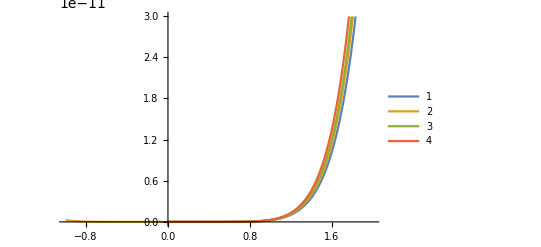

```mathematica
Plot[{V[ϕ]/.p->3.98,V[ϕ]/.p->4,V[ϕ]/.p->4.01,V[ϕ]/.p->4.03},{ϕ,-1,2},PlotLegends->Automatic]
```

Slow roll approximation for equation of motion for universe dominated by scalar field ϕ:
H^2= 1/3 V(ϕ)
3Hϕ’ = -V_ϕ

For obtaining value of ϕf:

```mathematica
ϵ= 1/2(V'[ϕ]/V[ϕ])^2//Expand//FullSimplify
```

(0.5 ⅇ^(4.60517 p) p^2 ϕ^(-2+2 p))/((-1.+10.^p ϕ^p)^2)

μ is taken as Plank mass

```mathematica
ϕflist1={};
ϕflist2={};
Do[ϵ1 =ϵ==1/.{p->i};
ϵsol =SolveValues[ϵ1,ϕ,Reals,Assumptions->ϕ>0 ];AppendTo[ϕflist1,{i,ϵsol[[1]]}];AppendTo[ϕflist2,{i,ϵsol[[2]]}],{i,3.94,4.06,0.01}]
```

```mathematica
ϕflist2//TableForm;
```

```mathematica
n = Integrate[V[ϕ]/V'[ϕ],{ϕ, ϕ,ϕi}]
```

ConditionalExpression[(-0.5 ϕ^2+0.5 ϕi^2-1. ⅇ^(-2.30259 p) (ϕ^(2-p)/(-2+p)-ϕi^(2-p)/(-2+p)))/p, ]

```mathematica
n =n//Normal//ExpandAll//FullSimplify
```

(-0.5 ϕ^2-(1. ⅇ^(-2.30259 p) ϕ^(2-p))/(-2.+p)+ϕi^2 (0.5+(1. ⅇ^(-2.30259 p) ϕi^-p)/(-2.+p)))/p

```mathematica
n1=n-60//FullSimplify;
```

```mathematica
phiidata ={}; 
Do[n2 =n1/.{ϕ->ϕflist2[[i,2]],p->ϕflist2[[i,1]]}//FullSimplify//N;
AppendTo[phiidata,FindRoot[n2,{ϕi,20}]],{i,Length[ϕflist2]}]
```

```mathematica
nsol1 =Table[{ϕflist2[[i,1]],ϕflist2[[i,2]],phiidata[[i,1,2]]},{i,Length[phiidata]}];
```

```mathematica
nsol1//TableForm
```

3.94 | 2.78601 | 21.9217
3.95 | 2.79308 | 21.95
3.96 | 2.80015 | 21.9782
3.97 | 2.80722 | 22.0064
3.98 | 2.81429 | 22.0345
3.99 | 2.82136 | 22.0626
4. | 2.82843 | 22.0907
4.01 | 2.8355 | 22.1188
4.02 | 2.84257 | 22.1468
4.03 | 2.84964 | 22.1748
4.04 | 2.85672 | 22.2027
4.05 | 2.86379 | 22.2306
4.06 | 2.87086 | 22.2585

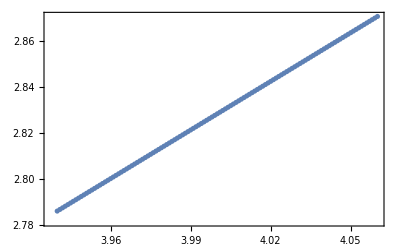

```mathematica
Table[{nsol1[[i,1]],nsol1[[i,2]]},{i,Length[nsol1]}]//ListPlot[#,Frame->True]&
```

For obtaining ϕ_sr:

```mathematica
g=-√3 Integrate[(√V[ϕ])/V'[ϕ],{ϕ,ϕi,ϕ}]
```

ConditionalExpression[-1/p1.68929×10^10 ⅇ^(-2.30259 p) (-1/((-2.+1. p) (-1.+10.^p ϕ^p))0.5 ϕ^(-1. p) √((-1.+10.^p ϕ^p)^2) (2. ϕ^2. Hypergeometric2F1[1.,-1.+2./p,2./p,1. 10.^p ϕ^p]+10.^p (-2.+1. p) ϕ^(2+1. p) Hypergeometric2F1[1.,2./p,(2.+p)/p,1. 10.^p ϕ^p])+1/((-2.+1. p) (-1.+10.^p ϕi^p))0.5 ϕi^(-1. p) √((-1.+10.^p ϕi^p)^2) (2. ϕi^2. Hypergeometric2F1[1.,-1.+2./p,2./p,1. 10.^p ϕi^p]+10.^p (-2.+1. p) ϕi^(2+1. p) Hypergeometric2F1[1.,2./p,(2.+p)/p,1. 10.^p ϕi^p])), ]

```mathematica
g1[ϕ_]:=g//Normal
```

```mathematica
g1[5]/.{p->4,ϕi->22.09072287850593,ϕ->5}
```

8013.75-1.47495×10^-8 ⅈ

```mathematica
ϕsrlist={};
Do[tre =FindRoot[g1[ϕ]-t/.{p->nsol1[[i,1]],ϕi->nsol1[[i,3]],t->0},{ϕ,20}];AppendTo[ϕsrlist,tre[[1,2]]],{i,Length[phiidata]}]
```

FindRoot::lstol: The line search decreased the step size to within tolerance specified by AccuracyGoal and PrecisionGoal but was unable to find a sufficient decrease in the merit function. You may need more than MachinePrecision digits of working precision to meet these tolerances.

General::munfl: (6.42627×10^-290)/(8.5408×10^37) is too small to represent as a normalized machine number; precision may be lost.

General::munfl: (1.54781×10^-288)/(5.73824×10^37) is too small to represent as a normalized machine number; precision may be lost.

FindRoot::lstol: The line search decreased the step size to within tolerance specified by AccuracyGoal and PrecisionGoal but was unable to find a sufficient decrease in the merit function. You may need more than MachinePrecision digits of working precision to meet these tolerances.

General::stop: Further output of FindRoot::lstol will be suppressed during this calculation.

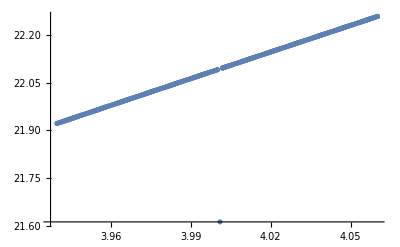

```mathematica
pvsϕsr =Table[{nsol1[[i,1]],ϕsrlist[[i]]},{i,Length[ϕsrlist]}];
pvsϕsr//ListPlot[#,Joined->False,Mesh->Full]&
```

```mathematica
derϕsr={};
Do[AppendTo[derϕsr, Re[ϕsrlist[[i+1]]-ϕsrlist[[i]]]/Abs[nsol1[[1,2]]-nsol1[[2,2]]]],{i,Length[ϕsrlist]}]
```

Part::partw: Part 122 of {21.9217-2.10797×10^-14 ⅈ,21.9245+5.82234×10^-14 ⅈ,21.9274+5.00933×10^-14 ⅈ,21.9302-4.74307×10^-14 ⅈ,21.933+2.29841×10^-13 ⅈ,21.9358-8.04404×10^-14 ⅈ,21.9387-1.22816×10^-13 ⅈ,21.9415+1.28155×10^-13 ⅈ,21.9443-7.32381×10^-14 ⅈ,21.9471+5.23638×10^-14 ⅈ,«111»} does not exist.

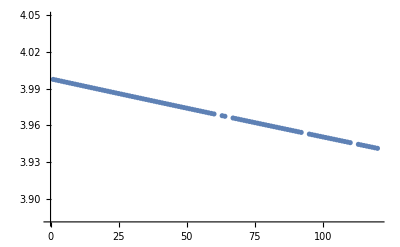

```mathematica
derϕsr//ListPlot
```

For obtaining a_sr:

```mathematica
asr= ⅇ^h;
h=√(1/3)Integrate[√(M^4 (1-(ϕ[t]/μ)^p)),{t,0,t}]
```

(∫_0^t 1.69×10^-10 √(1-(4.58716×10^7)^p ϕ[t]^p)ⅆt)/(√3)

```mathematica
asr
```

ⅇ^((∫_0^t 1.69×10^-10 √(1-(4.58716×10^7)^p ϕ[t]^p)ⅆt)/(√3))

```mathematica
hlist= Table[√(1/3)Integrate[√(M^4 (1-(ϕ[t]/μ)^p)),{t,0,t}]
```